```mathematica
'0.089-0.026-0.026 0.089-0.026 0.089 0.03375 0.03375 0.03375'
```

```mathematica
f[α1_,α11_,α12_,α111_,α112_,α123_,Px_,Py_,Pz_]:=α1(Px^2+Py^2+Pz^2)+α11(Px^4+Py^4+Pz^4)+α12(Px^2 Py^2+Py^2 Pz^2+Px^2 Pz^2)+α111(Px^6+Py^6+Pz^6)+α112(Px^4(Py^2+Pz^2)+Py^4(Px^2+Pz^2)+Pz^4(Px^2+Py^2))+α123 Px^2 Py^2 Pz^2
```

```mathematica
f[α1,α11,α12,α111,α112,α123,0,0,Pz]+Sum[q[i,j,k,l]e[i,j] P[k]P[l],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]/.{P[1]->Px,P[2]->Py,P[3]->Pz}/.{VT[q,q]}
```

{Pz^2 α1+Pz^4 α11+Pz^6 α111+Px^2 e[1,1] q[1,1]+Py^2 e[1,1] q[1,2]+Pz^2 e[1,1] q[1,3]+2 Py Pz e[1,1] q[1,4]+2 Px Pz e[1,1] q[1,5]+2 Px Py e[1,1] q[1,6]+Px^2 e[2,2] q[2,1]+Py^2 e[2,2] q[2,2]+Pz^2 e[2,2] q[2,3]+2 Py Pz e[2,2] q[2,4]+2 Px Pz e[2,2] q[2,5]+2 Px Py e[2,2] q[2,6]+Px^2 e[3,3] q[3,1]+Py^2 e[3,3] q[3,2]+Pz^2 e[3,3] q[3,3]+2 Py Pz e[3,3] q[3,4]+2 Px Pz e[3,3] q[3,5]+2 Px Py e[3,3] q[3,6]+Px^2 e[2,3] q[4,1]+Px^2 e[3,2] q[4,1]+Py^2 e[2,3] q[4,2]+Py^2 e[3,2] q[4,2]+Pz^2 e[2,3] q[4,3]+Pz^2 e[3,2] q[4,3]+2 Py Pz e[2,3] q[4,4]+2 Py Pz e[3,2] q[4,4]+2 Px Pz e[2,3] q[4,5]+2 Px Pz e[3,2] q[4,5]+2 Px Py e[2,3] q[4,6]+2 Px Py e[3,2] q[4,6]+Px^2 e[1,3] q[5,1]+Px^2 e[3,1] q[5,1]+Py^2 e[1,3] q[5,2]+Py^2 e[3,1] q[5,2]+Pz^2 e[1,3] q[5,3]+Pz^2 e[3,1] q[5,3]+2 Py Pz e[1,3] q[5,4]+2 Py Pz e[3,1] q[5,4]+2 Px Pz e[1,3] q[5,5]+2 Px Pz e[3,1] q[5,5]+2 Px Py e[1,3] q[5,6]+2 Px Py e[3,1] q[5,6]+Px^2 e[1,2] q[6,1]+Px^2 e[2,1] q[6,1]+Py^2 e[1,2] q[6,2]+Py^2 e[2,1] q[6,2]+Pz^2 e[1,2] q[6,3]+Pz^2 e[2,1] q[6,3]+2 Py Pz e[1,2] q[6,4]+2 Py Pz e[2,1] q[6,4]+2 Px Pz e[1,2] q[6,5]+2 Px Pz e[2,1] q[6,5]+2 Px Py e[1,2] q[6,6]+2 Px Py e[2,1] q[6,6]}

```mathematica
Solve[D[f[-0.172283,-0.07253,0.75,0.26,0.61,-3.67,0,0,Pz]+0.089*x*Pz^2,Pz]==0,Pz]
```

{{Pz→0.},{Pz→-0.00358057 √(7253.-1. √(1.39641×10^9-6.942×10^8 x))},{Pz→0.00358057 √(7253.-1. √(1.39641×10^9-6.942×10^8 x))},{Pz→-0.00358057 √(7253.+√(1.39641×10^9-6.942×10^8 x))},{Pz→0.00358057 √(7253.+√(1.39641×10^9-6.942×10^8 x))}}

```mathematica
Pz^2 α1+Pz^4 α11+Pz^6 α111+Pz^2 e[1,1] q[1,3]+Pz^2 e[2,2] q[2,3]+Pz^2 e[3,3] q[3,3]+Pz^2 e[2,3] q[4,3]+Pz^2 e[3,2] q[4,3]+Pz^2 e[1,3] q[5,3]+Pz^2 e[3,1] q[5,3]+Pz^2 e[1,2] q[6,3]+Pz^2 e[2,1] q[6,3]/.{e[1,3]->0,e[3,1]->0,e[2,3]->0,e[2,1]->0}
```

Pz^2 α1+Pz^4 α11+Pz^6 α111+Pz^2 e[1,1] q[1,3]+Pz^2 e[2,2] q[2,3]+Pz^2 e[3,3] q[3,3]+Pz^2 e[3,2] q[4,3]+Pz^2 e[1,2] q[6,3]

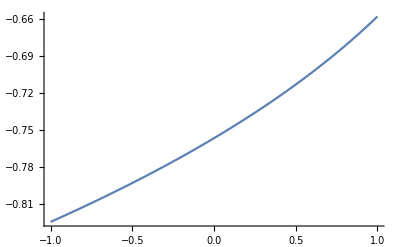

```mathematica
Plot[-0.003580574370197164 √(7253.+√(1.396413409*^9-6.942*^8 x)),{x,-1,1}]
```